# Projekt 2 Rapport

Kurskod: IX1501
Datum: 2017-11-29

Evan Saboo, saboo@kth.se
Max Kufa, mkufa@kth.se

Uppgift 1: Distribution Parameters

## Sammanfattning

### Uppgift

Uppgift 1 består av tre deluppgifter:

Estimera μ och σ från delvis slumpad data.

Testa de tre följande modellerna till den slumpade datan, och välj ut den som bäst representerar den slumpade datan.

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

Beräkna ett “Confidence Interval” på 95% för de valda konstanterna i den valda modellen. Intervallet får inte avvika mer än 10% från mellanvärdet, e.g. μ (1±0.05).

Den slumpade datan genereras från en fördefinierad fil vid namn “Projekt2.m”

### Resultat

#### Estimera μ och σ:

Genom att använda “Mean” och “StandardDeviation” så kan vi estimera μ och σ ur en lista av data genererad av “randomNumber” av storleken 1000:

μ = 5.19974
σ = 3.24391

#### Testa de tre modellerna:

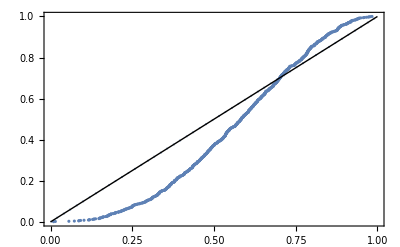
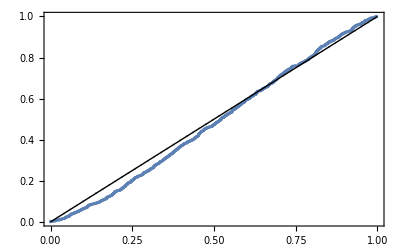
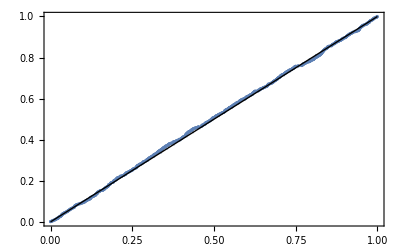
Vi använder oss av “ProbabilityDistribution” och “EstimatedDistribution” för att estimera våra matematiska funktioner som distributionsmodeller gentemot vår data. De olika kurvorna beter sig olika i jämförelse med vår datamängd 𝕩, och det gäller att hitta den modell som best passar in på 𝕩.
Följande grafer visar modellernas beteende i jämförelse med datamängden:

Modell e^(-a*x)
-Graphics-

Modell x*e^(-a*x)
-Graphics-

Modell x(x+b)*e^(-a*x)
-Graphics-

Vi ansåg att den sista modellen, x(x+b)*e^(-a*x), gav en funktion som bäst överrensstämmde med 𝕩. 
α och β fick värdena 4.32677 respektive 0.48208.

#### Beräkna “Confidence Interval”

Målet här är att hitta de gränsvärden för α och β som fortfarande ger ett “coinfidence interval” på 10%.
Vi bestämde oss för att använda α och β från den föregående uppgiften som hjälp för att hitta gränsvärdena, och använde metoden i sektion 2.2.3.2 i projektbeskrivningsfilen för att manuellt beräkna gränsvärderna genom att substituera μ med α och β.

Gränsvärderna för α respektive β blev därmed:
0.464813≤α≤0.53476
2.99036≤β≤3.0603

## Kod

```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]];
```

#### Uppgift 1

```mathematica
n=1000;
𝕩=randomNumber[0,n];
Short[𝕩]
```

{1.91606,12.8234,«997»,10.3068}

```mathematica
μ=Mean[𝕩]
σ=StandardDeviation[𝕩]
```

5.36906

3.39978

#### Uppgift 2

```mathematica
n=1000;
𝕩=randomNumber[0,n];
𝕩sort=Sort[𝕩];
```

```mathematica
f1[x_]:=ⅇ^(-a*x);
f2[x_]:=x*ⅇ^(-a*x);
f3[x_]:=x*(x+b)*ⅇ^(-a*x);
```

```mathematica
i1=Integrate[f1[x],{x,0,∞},Assumptions->{a>0}];
i2=Integrate[f2[x],{x,0,∞},Assumptions->{a>0}];
i3=Integrate[f3[x],{x,0,∞},Assumptions->{{a>0},{b>0}}];
```

```mathematica
c1=1/i1;
c2=1/i2;
c3=1/i3;
```

```mathematica
pdf1[x_]:=c1*f1[x]
pdf2[x_]:=c2*f2[x]
pdf3[x_]:=c3*f3[x]
```

```mathematica
𝒟1[a_]:=ProbabilityDistribution[pdf1[x],{x,0,∞},Assumptions->{a>0}]
𝒟2[a_]:=ProbabilityDistribution[pdf2[x],{x,0,∞},Assumptions->{a>0}]
𝒟3[a_,b_]:=ProbabilityDistribution[pdf3[x],{x,0,∞},Assumptions->{{a>0},{b>0}}]
```

```mathematica
myDist1=EstimatedDistribution[𝕩,𝒟1[a]];
myDist2=EstimatedDistribution[𝕩,𝒟2[a]];
myDist3=EstimatedDistribution[𝕩,𝒟3[a,b]];
```

ProbabilityDistribution[0.190622 ⅇ^(-0.190622 x),{x,0,∞},Assumptions→{True}]

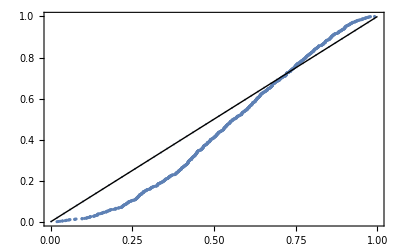

```mathematica
myDist1
ProbabilityPlot[𝕩,myDist1]
```

ProbabilityDistribution[0.145347 x ⅇ^(-0.381243 x),{x,0,∞},Assumptions→{True}]

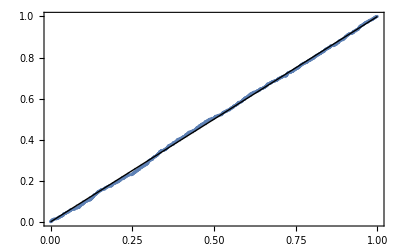

```mathematica
myDist2
ProbabilityPlot[𝕩,myDist2]
```

ProbabilityDistribution[0.0274209 x (4.32678+x) ⅇ^(-0.482083 x),{x,0,∞},Assumptions→{{True},{True}}]

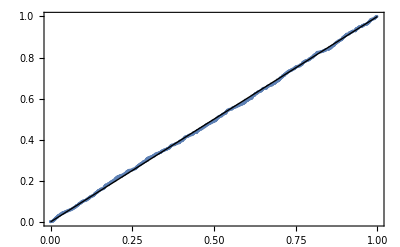

```mathematica
myDist3
ProbabilityPlot[𝕩,myDist3]
```

#### Uppgift 3

```mathematica
α=0.7173293780432751;
β=0.5393988397118393;
```

```mathematica
q=Quantile[myDist3,0.975];
```

```mathematica
s=StandardDeviation[𝕩];
```

```mathematica
n = 1000;
```

```mathematica
ciα = {α - q*(s/Sqrt[n]), α + q*(s/Sqrt[n])}
ciβ = {β- q*(s/Sqrt[n]), β + q*(s/Sqrt[n])}
```

{-0.957431,2.39209}

{-1.13536,2.21416}

```mathematica
Clear[α,β]
```

```mathematica
cilenα=ciα⟦2⟧-ciα⟦1⟧
cilenβ=ciβ⟦2⟧-ciβ⟦1⟧
```

3.34952

3.34952

```mathematica
margin=2;
nnew=Ceiling[margin*n*(cilenα/ 0.1)^2]
```

1725603

```mathematica
𝕩=randomNumber[0,nnew];
```

```mathematica
EstimatedDistribution[𝕩,𝒟3[a,b]]
```

ProbabilityDistribution[0.0355465 x (3.02533+x) ⅇ^(-0.499787 x),{x,0,∞},Assumptions→{{True},{True}}]

```mathematica
α=0.4997866602912788;
β=3.02533003422653;
```

```mathematica
s=StandardDeviation[𝕩]
```

3.35997

```mathematica
ciα = {α - q*(s/Sqrt[nnew]), α + q*(s/Sqrt[nnew])}
ciα = {β - q*(s/Sqrt[nnew]), β + q*(s/Sqrt[nnew])}
```

{0.464813,0.53476}

{2.99036,3.0603}

Uppgift 2: Which Distribution?

## Sammanfattning

I uppgift 2 ska vi använda fördelningarna i = 1,2,..., 6 i randomNumber funktionen och svara på dessa frågor:

Använd räta linjens metod för att bestäma en distributionsmodell för var och en av data-varianterna.

Estimera parametrarna för de olika distributionsmodellerna

Beräkna 95% konfidensintervaller för parametrarna. Intervallet bör inte vara längre än 10% av dess medelvärde.

### Resultat

#### Bestäm fördelningsmodell

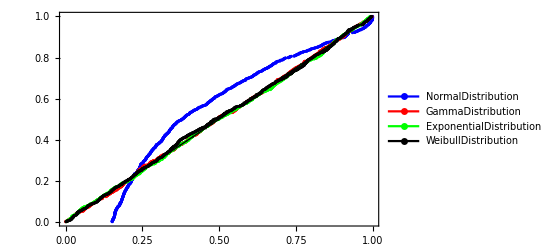
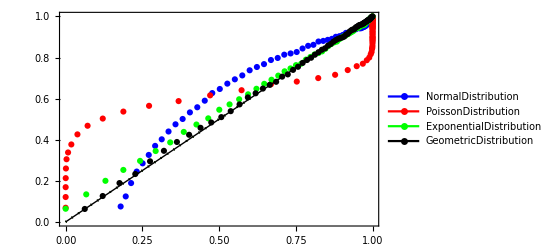
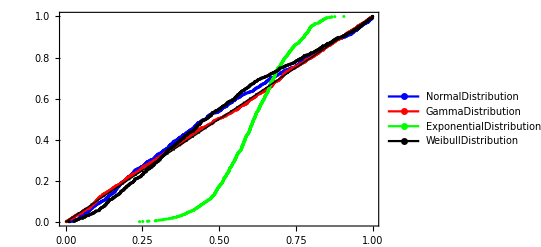
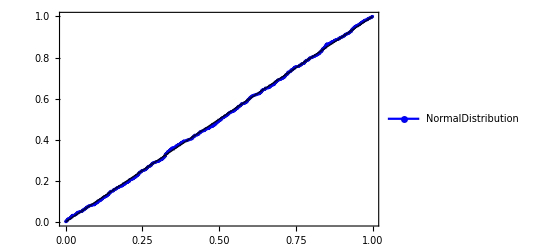
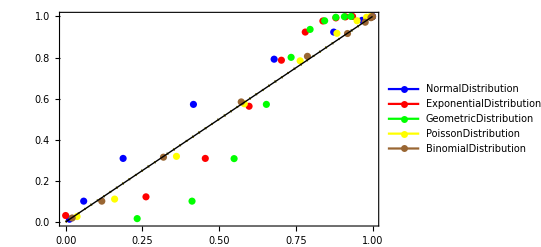
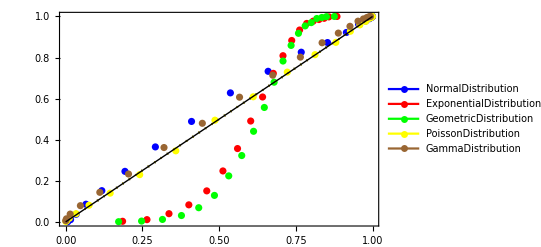
För att hitta den rätta fördelningsmodeller för varje fördelning i randomNumber funktionen testa vi alla inbyggda fördelningsmodeller och tog den som var närmast räta linjen.


1. Gamma fördelningsmodellen för den första fördelningen. 
-Graphics-

2.  Geometriska fördelningsmodellen för andra fördelningen. 
-Graphics-

3.  Gamma Distributions modellen för tredje fördelningen.
-Graphics-

4. Normalfördelningsmodellen för fjärde fördelningen.
-Graphics-

5. Poissonfördelningsmodellen för femte fördelningen.
-Graphics-

6. Poissonfördelningsmodellen för sjätte fördelningen.
-Graphics-

#### Estimera parametrarna

Eftersom vi fick ut fördelningsmodell för fördelning så kan vi också få estimera parametrarna med hjälpa av inbyggda funktionen “EstimateDistribution”.
Vi fick parametrarna:

Distribution 1:
GammaDistribution[0.970294,0.216259]

Distribution 2:
GeometricDistribution[0.0690512]

Distribution 3:
GammaDistribution[7.96105,1.61395]

Distribution 4:
NormalDistribution[2.98273,5.15498]

Distribution 5:
PoissonDistribution[3.275]

Distribution 6:
PoissonDistribution[9.758]

#### Beräkna konfidensintervaller

För att få ut konfidensintervaller för varje fördelning tog först få ut {α,β} eller bara {α} (beroende på distributionsmodellen) med hjälp av  EstimatedDistribution och sedan använda Central Limit Theorem för att få ut intervallerna för α och β.
Vi kom fram till:
Distribution 1:
0.964902 < α <1.01956
0.213129 < β <1.01956 

Distribution 2:
0.0631177 < α <0.0654572

Distribution 3:
7.76802 < α <8.49892
1.52164 < β <1.61731 

Distribution 4:
2.96675 < α <3.15467
4.9226 < β <5.26378 

Distribution 5:
3.14326 < α <3.29407

Distribution 6:
9.54735 < α <10.0513

Genom att repitera uträckningen antal gånger så fick vi ut intervaller  som är längre än 10% av dess medelvärde.

## Uträkning

#### Bestäm fördelningsmodell

För hitta den rätta fördelningsmodellen för varje fördelning användes inbyggda funktionen EstimatedDistribution, som tog emot en lista av punkter (vår generade slumpvisa punkter)och en distributionsmodell.
Svaret från EstimatedDistribution lades in i ProbilityPlot funktionen med alla tagna punkter från randomNumber för att jämföra punkterna med fördelningsmodellen.

Vi hade tju modeller o välja mellan för varje fördelning, några fungerade att plotta ut medan andra kunde vi inte ens få ut eftersom vi fick felmeddelanden när vi försökte räkna ut dem.
De sju modellerna var normal-, gamma-, exponential-, weibull, geometrisk-, poisson- och binomialfördelning.


-Graphics-
Vi kunde plotta ut fyra fördelningsmodeller för den första fördelningen. Man kan så att tre av dem är ganska lika varandra men den som är närmast räta linjen är gamma fördelningen.



-Graphics-
För den andra fördelningen kunde också få ut fyra modeller. Man kan se att den bästa fördelningsmodellen är gemotriska fördelningen.




-Graphics-
Gamma fördelningen passar bäst för den tredje fördelningen i randomNumber funktionen



-Graphics-
Vi kunde bara få ut normal fördelningen för den fjärde fördelningen och vi kan se att modellen passar bra med fördelningen. 


-Graphics-
Man kan se att binomal fördelningen passar bäst för den femte fördelningen men vi kunde inte välja modellen eftersom i uppgift 6 (konfidensintervall) så fick vi felmeddelenade ibland när vi försökte ränka med binomial fördelningsmodellen.
Därför tog vi poisson fördelningen den bästa modell till femte fördelningen. 



-Graphics-
 I grafen kan man se att poisson fördelningen är närmast räta linjen. Med det kan vi konstantera att den bästa modellen för sjätte fördelningen är poisson fördelning.

#### Beräkna konfidensintervaller

För att räkna ut konfidensintervaller för fördelningarna användes metoder tagna från  Hypothesis Testing Package.

Vi har skapat en metod som får ut {α,β}  genom EstimatedDistribution och använder sedan CLT (MeanCI metoden) för att få ut intervaller för α och β.
Detta görs om flera gånger tills CLT ger oss intervaller som inte är längre än dess medelvärde.

## Kod

### Uppgift 4

```mathematica
dist1[i_,n_, a_, plotName_, color_] := 
Module[{𝕩, 𝒩, plot, μ, σ},
𝕩=randomNumber[i,n];
𝒩=EstimatedDistribution[𝕩,a];

plot =ProbabilityPlot[𝕩,𝒩, PlotLegends->LineLegend[{color},{plotName}], PlotStyle->color];
{𝕩, plot}
]
```

```mathematica
n = 1000;
```

```mathematica
normalD = NormalDistribution[a,b];
gammaD = GammaDistribution[a,b];
expD = ExponentialDistribution[a];
weibullD = WeibullDistribution[a,b]; 
geoD = GeometricDistribution[a];
poissonD = PoissonDistribution[a];
binD = BinomialDistribution[a,b];
```

```mathematica
(*Distribution 1*)
```

```mathematica
{𝕩11, plot11} = dist1[1,n,normalD,"NormalDistribution", Blue ];
{𝕩12, plot12} = dist1[1,n, gammaD, "GammaDistribution", Red];
{𝕩13, plot13} = dist1[1,n, expD,"ExponentialDistribution", Green ];
{𝕩14, plot14} = dist1[1,n, weibullD,"WeibullDistribution", Black ];
```

```mathematica
(*Distribution 2*)
```

```mathematica
{𝕩21, plot21} = dist1[2,n, normalD,"NormalDistribution", Blue ];
{𝕩22, plot22} = dist1[2,n, poissonD, "PoissonDistribution", Red];
{𝕩23, plot23} = dist1[2,n, expD,"ExponentialDistribution", Green ];
{𝕩24, plot24} = dist1[2,n,geoD,"GeometricDistribution", Black ];
```

```mathematica
(*Distribution 3*)
```

```mathematica
{𝕩31, plot31} = dist1[3,n,normalD,"NormalDistribution", Blue ];
{𝕩32, plot32} = dist1[3,n, gammaD, "GammaDistribution", Red];
{𝕩33, plot33} = dist1[3,n, expD,"ExponentialDistribution", Green ];
{𝕩34, plot34} = dist1[3,n, weibullD,"WeibullDistribution", Black ];
```

```mathematica
(*Distribution 4*)
```

```mathematica
{𝕩41, plot41} = dist1[4,n,normalD,"NormalDistribution", Blue ];
```

```mathematica
(*Distribution 5*)
```

```mathematica
{𝕩51, plot51} = dist1[5,n,normalD,"NormalDistribution", Blue ];
{𝕩52, plot52} = dist1[5,n,expD,"ExponentialDistribution", Red ];
{𝕩53, plot53} = dist1[5,n,geoD,"GeometricDistribution", Green ];
{𝕩54, plot54} = dist1[5,n,poissonD,"PoissonDistribution", Yellow ];
{𝕩55, plot55} = dist1[5,n,binD,"BinomialDistribution", Brown ];
```

```mathematica
(*Distribution 6*)
```

```mathematica
{𝕩61, plot61} = dist1[6,n,normalD,"NormalDistribution", Blue ];
{𝕩62, plot62} = dist1[6,n,expD,"ExponentialDistribution", Red ];
{𝕩63, plot63} = dist1[6,n,geoD,"GeometricDistribution", Green ];
{𝕩64, plot64} = dist1[6,n,poissonD,"PoissonDistribution", Yellow ];
{𝕩65, plot65} = dist1[6,n,gammaD,"GammaDistribution", Brown ];
```

```mathematica
(*GammaDistribution for Distribution 1*)
```

```mathematica
Show[plot11,plot12, plot13, plot14]
```

-Graphics-

```mathematica
(*GeometricDistribution for Distribution 2*)
```

```mathematica
Show[plot21,plot22, plot23, plot24]
```

-Graphics-

```mathematica
(*GammaDistribution for Distribution 3*)
```

```mathematica
Show[plot31,plot32, plot33, plot34]
```

-Graphics-

```mathematica
(*NormalDistribution for Distribution 4*)
```

```mathematica
plot41
```

-Graphics-

```mathematica
(*BinomialDistribution for Distribution 5*)
```

```mathematica
Show[plot51,plot52, plot53, plot54, plot55]
```

-Graphics-

```mathematica
(*PoissonDistribution for Distribution 6*)
```

```mathematica
Show[plot61,plot62, plot63, plot64, plot65]
```

-Graphics-

### Uppgift 5

```mathematica
(*Distribution 1*)
```

```mathematica
EstimatedDistribution[𝕩12,gammaD]
```

GammaDistribution[0.970294,0.216259]

```mathematica
(*Distribution 2*)
```

```mathematica
EstimatedDistribution[𝕩24,geoD]
```

GeometricDistribution[0.0690512]

```mathematica
(*Distribution 3*)
```

```mathematica
EstimatedDistribution[𝕩32,gammaD]
```

GammaDistribution[7.96105,1.61395]

```mathematica
(*Distribution 4*)
```

```mathematica
EstimatedDistribution[𝕩41,normalD]
```

NormalDistribution[2.98273,5.15498]

```mathematica
(*Distribution 5*)
```

```mathematica
EstimatedDistribution[𝕩54,poissonD]
```

PoissonDistribution[3.275]

```mathematica
(*Distribution 6*)
```

```mathematica
EstimatedDistribution[𝕩64,poissonD]
```

PoissonDistribution[9.758]

### Uppgift 6

```mathematica
Needs["HypothesisTesting`"]
```

En metod som tar ut konfidensintervall för α som inte är längre än 10% av dess medelvärde

```mathematica
cltαβ[d_, m_,a_] := 
Module[{i=1 , j=1,n=2,𝕩, 𝕒,𝕓, findαβ, ciα1, ciα2, ciβ1, ciβ2, m𝕒,m𝕓},
findαβ[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 || j == 1,
𝕩=randomNumber[d,{n,m}];
{𝕒,𝕓} = Transpose[findαβ/@𝕩];
m𝕒 = Mean[𝕒];
m𝕓 = Mean[𝕓];
If[i ≠ 0,
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
 0];
If[j≠ 0,
{ciβ1, ciβ2}=MeanCI[𝕓, ConfidenceLevel->0.95];
0];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
Which[ciβ1 ≥ m𝕓 *0.95&& m𝕓 *1.05 ≥ ciβ2,  j=0]; 
n++;];
{{ciα1, ciα2}, {ciβ1, ciβ2} }
]
```

En metod som tar ut konfidensintervall för α och β som inte är längre än 10% av dess medelvärde

```mathematica
cltα[d_, m_,a_] := 
Module[{i=1 ,n=2,𝕩, 𝕒, findα, ciα1, ciα2, m𝕒},
findα[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 ,
𝕩=randomNumber[d,{n,m}];
{𝕒} = Transpose[findα/@𝕩];
m𝕒 = Mean[𝕒];
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
n++;];
{ciα1, ciα2}
]
```

```mathematica
cltαβ[1, n, gammaD]
```

{{0.964902,1.01956},{0.213129,0.231411}}

```mathematica
cltα[2, n, geoD ]
```

{0.0631177,0.0654572}

```mathematica
cltαβ[3, n, gammaD]
```

{{7.76802,8.49892},{1.52164,1.61731}}

```mathematica
cltαβ[4, n, normalD]
```

{{2.96675,3.15467},{4.9226,5.26378}}

```mathematica
cltαβ[5, n,binD]
```

{{10.9128,11.9205},{0.277445,0.303625}}

```mathematica
cltα[5, n,poissonD]
```

{3.14326,3.29407}

```mathematica
cltα[6, n, poissonD]
```

{9.54735,10.0513}